## “NISTEP-DSlink-Target_NEW-16” ver. 3

## 論文

https://niilan-my.sharepoint.com/personal/amano_nii_ac_jp/_layouts/15/doc.aspx?sourcedoc={605107e9-cdb9-43f4-a476-875350b9c0b7}&action=edit

上記はNIIアカウントでないとアクセスできない。

## Program

```mathematica
countNormal[list_]:=list/Tr[list]
```

```mathematica
listToSVstr[l_List]:=StringJoin[Riffle[Map[ToString,l]," "]]
```

```mathematica
toSVstrLines[l_List]:=StringJoin[Riffle[l,"\n"]]
```

```mathematica
matToSVstrLines[m_List]:=toSVstrLines[Map[listToSVstr,m]]
```

```mathematica
matTokmeansSV[m_List]:=Module[{size,mat},
size=Reverse[Dimensions[m]];
mat=Prepend[m,size];
matToSVstrLines[mat]<>"\n"
]
```

```mathematica
textPadding[string_,total_,char_]:=Module[{len,pad,padstr},
len=StringLength[string];
pad=Max[Ceiling[(total-len)/2],0];
padstr=StringJoin[Table[char,{pad}]];
StringJoin[padstr,string,padstr]
]
```

```mathematica
textPaddingR[string_,total_,char_]:=Module[{len,pad,padstr},
len=StringLength[string];
pad=total-len;
padstr=StringJoin[Table[char,{pad}]];
StringJoin[string,padstr]
]
```

```mathematica
textPadding["11",8," "]
```

11

## Data

```mathematica
dir="/Volumes/home/NII/基盤_CiNii/研究開発/ディスカバリサービス/NISTEP"
```

/Volumes/home/NII/基盤_CiNii/研究開発/ディスカバリサービス/NISTEP

```mathematica
datadir=dir<>"/NISTEP-DSlink-Target_New-16/"
```

/Volumes/home/NII/基盤_CiNii/研究開発/ディスカバリサービス/NISTEP/NISTEP-DSlink-Target_New-16/

```mathematica
SetDirectory[dir]
```

/Volumes/home/NII/基盤_CiNii/研究開発/ディスカバリサービス/NISTEP

```mathematica
(tsv=Import[datadir<>"selected-services.new.tsv"])//Dimensions
```

{66,64}

項目名

```mathematica
tsv[[1]]
```

{,,,調査対象URL,,,,項目の説明：
階層：<数字>/<*>/<**>
<アルファベット>は「NISTEP-DSlink-Target」シートのカラム番号に相当。,1. オートコンプリート,**サジェスト,**スペルチェック,2.ベストファースト = O:ソート,* 関連度,* 人気度,* 日付,* フォーマット（ソースの）,* パーソナライズ,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）,**スコア,3. 横断検索,**エンジン（マルチエンジン）,4. ファセット型ナビ = ファセット型ナビ,L:ビルダー形式GUI,5.詳細検索 = K:詳細検索,J:検索box,6.パーソナライズ,X:login機能,**適合性のチューニング,**利用状況、利用コンテキスト,**訪問済み、履歴,**タグ、メモ、コメント,7.ページネーション = ページネーション,Q:全件表示,8. 構造化された結果（結果にふさわしい表示、Wolfram Alphaの例）,**ハイライト,**クラスタリング,**テキスト解析,V:データプロット,U:マップ,S:サムネイル,削除項目,9. アクション可能な結果（computable）,W:ロケータ/スライダ等、GUIによる指定,**パールグローイング（検索結果から次のクエリー（検索語）を導く）,N:検索結果リファイン,10. 統合的発見（システムの多機能性を利用した発見）,**レコメン,**セレンディピティ,**トピック,**曖昧性回避,11. NISTEPサービスにあるが本書にない項目（空項目）,R:バリアフリー,P:ダウンロード,M:検索対象のタイプ,T:ダウンロードのデータ形式,Y:利用統計,Z1:API,Z:その他,仕掛かり中,除外,完,担当,ジャンル,表示名}

項目範囲

```mathematica
itemStart=9
itemEnd=57
```

9

57

```mathematica
(tsvBody=Drop[tsv,2])//Dimensions
```

{64,64}

```mathematica
(tsvEvalBody=Map[#[[Range[itemStart,itemEnd]]]&,tsvBody])//Dimensions
```

{64,49}

```mathematica
(tsvEvalHead=tsv[[1]][[Range[itemStart,itemEnd]]])//Length
```

49

サイトID

```mathematica
tsvBodyID=Map[#[[1]]&,tsvBody]
```

{1,2,4,5,6,7,8,15,16,18,19,20,21,22,23,24,25,26,27,28,32,35,36,37,38,42,43,46,48,53,54,55,57,58,59,60,61,62,63,64,66,67,68,69,70,71,72,73,74,76,77,82,83,84,85,86,90,91,93,103,104,105,106,108}

サイト名+地域+ジャンル

```mathematica
tsvBodySite=Map[#[[-1]]<>"  :"<>#[[6]]<>":"<>#[[-2]]&,tsvBody]
```

{国民経済計算  :日本:経済・産業統計/報告,科学技術関係活動に関する調査  :日本:経済・産業統計/報告,科学技術研究調査  :日本:学術統計,経済センサス  :日本:経済・産業統計/報告,事業所・企業統計調査  :日本:経済・産業統計/報告,科学研究費補助金　配分結果  :日本:補助金情報,国際研究交流の概況  :日本:教育・学校統計/報告,科学技術システムの意識定点調査  :日本:経済・産業統計/報告,全国イノベーション調査  :日本:経済・産業統計/報告,J-GLOBAL  :日本:学術総合,researchmap  :日本:学術総合,外国人留学生在籍状況調査  :日本:学生支援,大学ポートレート  :日本:大学情報,大学基本情報  :日本:大学情報,CiNii Articles  :日本:学術論文,KAKEN  :日本:補助金情報,厚生労働科学研究成果データベース  :日本:学術総合,賃金構造基本統計調査  :日本:経済・産業統計/報告,品種登録／出願公表データ  :日本:特許等,経済産業省企業活動基本調査  :日本:経済・産業統計/報告,JIPデータベース  :日本:経済・産業統計/報告,成果報告書データベース  :日本:学術総合,知的財産活動調査  :日本:特許等,特許プラットフォーム  :日本:特許等,IIPパテントデータベース  :日本:特許等,指標情報データベース  :日本:学術総合,Orbis  :世界:経済・産業統計/報告,Main Science and Technology Indicators  :世界:経済・産業統計/報告,Research and Development Statistics  :世界:経済・産業統計/報告,WIPO IP Statistics Data Center  :世界:特許等,World Bank Open Data  :世界:経済・産業統計/報告,Espacenet  :欧州:特許等,Eurostat  :欧州:経済・産業統計/報告,eSearch plus  :欧州:特許等,publicdata.eu  :欧州:医療健康,RISIS Datasets  :欧州:学術総合,Data.gov.uk  :英国:学術総合,Science, engineering and technology Statistics  :英国:学術総合,UNISTATS  :英国:大学情報,Finances of Higher Education Providers  :英国:教育・学校統計/報告,ONS Gross Domestic Expenditure  :英国:経済・産業統計/報告,英国特許庁データベース  :英国:特許等,CWTS Leiden Ranking  :蘭国:学術統計,University-Industry Research Connections  :蘭国:その他,ライデン声明  :蘭国:その他,Bundesbericht Forschung und Innovation  :独国:教育・学校統計/報告,Daten Potal  :独国:教育・学校統計/報告,Förderatlas 2015  :独国:補助金情報,ドイツ特許庁　特許検索データベース  :独国:特許等,ドイツ特許庁統計情報  :独国:特許等,Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告,Evaluation Procedures  :仏国:教育・学校統計/報告,data.gouv.fr  :仏国:学術総合,Bases de données gratuites  :仏国:経済・産業統計/報告,Statistiques structurelles  :仏国:経済・産業統計/報告,Repères et références statistiques  :仏国:教育・学校統計/報告,Data.gov  :米国:学術総合,National Bureau of Economic Research  :米国:経済・産業統計/報告,Academic Institution Profiles  :米国:学術総合,WebCASPAR  :米国:学術総合,Science and Engineering Indicators  :米国:学術統計,FedScope-Federal Human Resources Data  :米国:経済・産業統計/報告,米国特許検索データベース  :米国:特許等,サンフランシスコ宣言  :米国:その他}

## Binary Mat

```mathematica
(tsvBinaryBody=(tsvEvalBody/.{""->0,(x_/;StringLength[x]>0)->1}))//Dimensions
```

StringLength::string: StringLength[0]の位置1で文字列が想定されています．

StringLength::string: StringLength[1]の位置1で文字列が想定されています．

General::stop: この計算中に，StringLength::stringのこれ以上の出力は表示されません．

{64,49}

## ゼロカウント項目の除去

```mathematica
Map[Tr,tsvBinaryBody//Transpose]
```

{0,15,0,37,28,2,36,3,0,4,4,0,28,25,3,45,60,0,8,25,0,0,0,51,17,0,22,1,0,4,3,15,0,0,1,0,20,0,6,0,5,0,62,1,17,64,14,0,7}

```mathematica
dp=Position[Map[Tr,tsvBinaryBody//Transpose],0]
```

{{1},{3},{9},{12},{18},{21},{22},{23},{26},{29},{33},{34},{36},{38},{40},{42},{48}}

除外する項目名

```mathematica
(dpname=tsvEvalHead[[Flatten[dp]]])
```

{1. オートコンプリート,**スペルチェック,* パーソナライズ,3. 横断検索,6.パーソナライズ,**利用状況、利用コンテキスト,**訪問済み、履歴,**タグ、メモ、コメント,8. 構造化された結果（結果にふさわしい表示、Wolfram Alphaの例）,**テキスト解析,削除項目,9. アクション可能な結果（computable）,**パールグローイング（検索結果から次のクエリー（検索語）を導く）,10. 統合的発見（システムの多機能性を利用した発見）,**セレンディピティ,**曖昧性回避,Y:利用統計}

採用する項目名

```mathematica
(tsvEvalHeadDrop=Delete[tsvEvalHead,dp])
```

{**サジェスト,2.ベストファースト = O:ソート,* 関連度,* 人気度,* 日付,* フォーマット（ソースの）,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）,**スコア,**エンジン（マルチエンジン）,4. ファセット型ナビ = ファセット型ナビ,L:ビルダー形式GUI,5.詳細検索 = K:詳細検索,J:検索box,X:login機能,**適合性のチューニング,7.ページネーション = ページネーション,Q:全件表示,**ハイライト,**クラスタリング,V:データプロット,U:マップ,S:サムネイル,W:ロケータ/スライダ等、GUIによる指定,N:検索結果リファイン,**レコメン,**トピック,11. NISTEPサービスにあるが本書にない項目（空項目）,R:バリアフリー,P:ダウンロード,M:検索対象のタイプ,T:ダウンロードのデータ形式,Z1:API}

```mathematica
tsvEvalHeadDrop//Dimensions
```

{32}

メモ：サジェストとレコメンの違い：れこめんは検索語の提案等（関連）、サジェストはオートコンプリートや検索式変換など。

採用項目による行列

```mathematica
(tsvBinaryBodyZDrop=Transpose[Delete[Transpose[tsvBinaryBody],dp]])//Dimensions
```

{64,32}

### 評価軸の交絡（相関）の確認

```mathematica
(binaryCorrMap=ReplacePart[((Correlation[tsvBinaryBodyZDrop]//N)/.Indeterminate->0),Table[{i,i}->0,{i,50}]])//Dimensions
```

{32,32}

```mathematica
binaryCorrMap//MatrixForm
```

(0 | 0.173884 | 0.255593 | 0.112622 | 0.264887 | -0.1227 | 0.161905 | 0.161905 | 0.181239 | 0.31304 | 0.0518065 | 0.278783 | 0.142857 | 0.0139414 | 0.31304 | 0.00429755 | 0.0848196 | 0.143187 | -0.0697071 | 0.00952381 | 0.0518065 | -0.044898 | -0.0697071 | 0.343182 | 0.0751364 | 0.113821 | 0.0993726 | -0.0697071 | -0.165724 | 0 | 0.0641306 | -0.193892
0.173884 | 0 | 0.753371 | 0.153426 | 0.904842 | 0.189442 | 0.220564 | 0.0898596 | 0.179374 | 0.42455 | -0.109923 | 0.483662 | 0.17155 | 0.0358748 | 0.554246 | 0.276467 | 0.155582 | 0.285188 | -0.147485 | 0.0898596 | 0.189442 | 0.0991956 | 0.107624 | 0.371155 | 0.166209 | 0.130787 | 0.0284123 | 0.107624 | 0.0123122 | 0 | -0.00717496 | -0.00475173
0.255593 | 0.753371 | 0 | 0.203653 | 0.777778 | 0.102446 | 0.16265 | -0.22771 | 0.111111 | 0.326823 | -0.19558 | 0.36624 | 0.22771 | 0.047619 | 0.714168 | 0.288686 | 0.182743 | 0.290129 | -0.111111 | 0.03253 | 0.102446 | 0.03253 | 0.142857 | 0.356753 | 0.25664 | 0.212724 | 0.158397 | 0.142857 | -0.173828 | 0 | -0.00952381 | -0.0063073
0.112622 | 0.153426 | 0.203653 | 0 | 0.158397 | 0.385027 | -0.0463739 | -0.0463739 | 0.203653 | 0.224327 | -0.0398304 | -0.0798508 | 0.0463739 | -0.0678844 | 0.224327 | 0.0906788 | 0.298637 | -0.129989 | -0.0226281 | -0.0463739 | 0.385027 | -0.0993726 | -0.0226281 | 0.266398 | 0.250324 | 0.28234 | 0.0322581 | -0.0226281 | 0.298637 | 0 | 0.339422 | 0.224788
0.264887 | 0.904842 | 0.777778 | 0.158397 | 0 | 0.19558 | 0.09759 | 0.09759 | 0.269841 | 0.383311 | -0.251459 | 0.529971 | 0.29277 | 0.047619 | 0.576984 | 0.415903 | 0.173828 | 0.373024 | -0.142857 | -0.03253 | 0.0465666 | 0.190533 | 0.111111 | 0.254824 | 0.175596 | 0.139371 | 0.203653 | 0.111111 | -0.0401143 | 0 | -0.0666667 | 0.0063073
-0.1227 | 0.189442 | 0.102446 | 0.385027 | 0.19558 | 0 | -0.0572598 | -0.0572598 | 0.251459 | 0.276986 | -0.0491803 | -0.0176966 | 0.0572598 | -0.0838198 | 0.125472 | 0.111965 | 0.201369 | -0.160503 | -0.0279399 | -0.0572598 | 0.300546 | -0.1227 | -0.0279399 | 0.00996766 | 0.182282 | 0.486342 | 0.0398304 | -0.0279399 | 0.201369 | 0 | 0.240283 | 0.395979
0.161905 | 0.220564 | 0.16265 | -0.0463739 | 0.09759 | -0.0572598 | 0 | 0.2 | -0.09759 | 0.190187 | 0.248126 | 0.167774 | -0.2 | 0.09759 | 0.0578829 | -0.0300828 | 0.137016 | -0.0509647 | -0.03253 | 0.2 | 0.248126 | -0.142857 | -0.03253 | 0.382971 | -0.0830455 | 0.405889 | 0.0463739 | -0.03253 | -0.00913442 | 0 | 0.019518 | -0.0904828
0.161905 | 0.0898596 | -0.22771 | -0.0463739 | 0.09759 | -0.0572598 | 0.2 | 0 | 0.16265 | 0.190187 | 0.248126 | 0.167774 | -0.2 | 0.09759 | -0.206725 | -0.0300828 | -0.155285 | 0.220847 | -0.03253 | 0.2 | 0.248126 | 0.161905 | -0.03253 | -0.0348155 | -0.0830455 | -0.0751646 | 0.0463739 | -0.03253 | 0.137016 | 0 | 0.019518 | 0.116335
0.181239 | 0.179374 | 0.111111 | 0.203653 | 0.269841 | 0.251459 | -0.09759 | 0.16265 | 0 | 0.39138 | 0.102446 | 0.228361 | 0.22771 | 0.047619 | 0.262265 | 0.288686 | -0.102514 | 0.0911835 | 0.142857 | -0.09759 | -0.0465666 | 0.181239 | -0.111111 | 0.220847 | 0.25664 | 0.212724 | 0.158397 | 0.142857 | 0.111429 | 0 | 0.219048 | 0.0946095
0.31304 | 0.42455 | 0.326823 | 0.224327 | 0.383311 | 0.276986 | 0.190187 | 0.190187 | 0.39138 | 0 | 0.276986 | 0.309957 | 0.0744208 | 0.0847319 | 0.34359 | 0.165422 | 0.243592 | -0.0400355 | -0.100871 | 0.32249 | 0.276986 | -0.0649706 | 0.157359 | 0.634795 | 0.291848 | 0.244263 | 0.143799 | -0.100871 | 0.171081 | 0 | 0.196094 | 0.129866
0.0518065 | -0.109923 | -0.19558 | -0.0398304 | -0.251459 | -0.0491803 | 0.248126 | 0.248126 | 0.102446 | 0.276986 | 0 | 0.144101 | -0.248126 | -0.0838198 | -0.177555 | -0.25551 | -0.133374 | -0.160503 | -0.0279399 | 0.553512 | 0.300546 | -0.1227 | -0.0279399 | 0.16945 | 0.182282 | 0.210892 | 0.0398304 | -0.0279399 | 0.0339973 | 0 | 0.419099 | -0.0777154
0.278783 | 0.483662 | 0.36624 | -0.0798508 | 0.529971 | -0.0176966 | 0.167774 | 0.167774 | 0.228361 | 0.309957 | 0.144101 | 0 | 0.256076 | 0.0387783 | 0.309957 | 0.266966 | -0.151235 | 0.182262 | 0.0818654 | 0.167774 | -0.0176966 | 0.359516 | 0.0818654 | 0.142954 | 0.208993 | 0.0617259 | 0.276407 | 0.0818654 | 0.235927 | 0 | 0.17838 | 0.118135
0.142857 | 0.17155 | 0.22771 | 0.0463739 | 0.29277 | 0.0572598 | -0.2 | -0.2 | 0.22771 | 0.0744208 | -0.248126 | 0.256076 | 0 | 0.09759 | 0.206725 | 0.511408 | 0.155285 | 0.186871 | 0.03253 | -0.2 | -0.248126 | 0.142857 | 0.03253 | 0.0348155 | 0.0830455 | 0.0751646 | -0.0463739 | 0.03253 | -0.137016 | 0 | -0.019518 | 0.0904828
0.0139414 | 0.0358748 | 0.047619 | -0.0678844 | 0.047619 | -0.0838198 | 0.09759 | 0.09759 | 0.047619 | 0.0847319 | -0.0838198 | 0.0387783 | 0.09759 | 0 | 0.0847319 | 0.190826 | -0.0133714 | -0.0746047 | 0.333333 | -0.09759 | -0.0838198 | -0.209121 | -0.047619 | 0.152894 | 0.040522 | -0.11003 | 0.0678844 | -0.047619 | -0.0133714 | 0 | -0.2 | 0.0189219
0.31304 | 0.554246 | 0.714168 | 0.224327 | 0.576984 | 0.125472 | 0.0578829 | -0.206725 | 0.262265 | 0.34359 | -0.177555 | 0.309957 | 0.206725 | 0.0847319 | 0 | 0.165422 | 0.243592 | 0.162249 | -0.100871 | -0.0744208 | 0.125472 | 0.0862337 | 0.157359 | 0.427515 | 0.0721037 | 0.124928 | 0.143799 | 0.157359 | 0.0985697 | 0 | 0.118625 | 0.0272559
0.00429755 | 0.276467 | 0.288686 | 0.0906788 | 0.415903 | 0.111965 | -0.0300828 | -0.0300828 | 0.288686 | 0.165422 | -0.25551 | 0.266966 | 0.511408 | 0.190826 | 0.165422 | 0 | 0.303642 | 0.201867 | 0.0636087 | -0.190525 | -0.0717724 | 0.18766 | 0.0636087 | 0.00523675 | 0.0291462 | 0.00226116 | 0.35574 | 0.0636087 | 0.0398445 | 0 | -0.0146789 | 0.176929
0.0848196 | 0.155582 | 0.182743 | 0.298637 | 0.173828 | 0.201369 | 0.137016 | -0.155285 | -0.102514 | 0.243592 | -0.133374 | -0.151235 | 0.155285 | -0.0133714 | 0.243592 | 0.303642 | 0 | -0.211818 | -0.0757714 | -0.00913442 | 0.0339973 | -0.249239 | 0.209486 | 0.281447 | 0.0493072 | 0.220394 | 0.108018 | -0.0757714 | 0.118899 | 0 | 0.0240686 | 0.129289
0.143187 | 0.285188 | 0.290129 | -0.129989 | 0.373024 | -0.160503 | -0.0509647 | 0.220847 | 0.0911835 | -0.0400355 | -0.160503 | 0.182262 | 0.186871 | -0.0746047 | 0.162249 | 0.201867 | -0.211818 | 0 | -0.0911835 | 0.0849412 | -0.00486372 | 0.0655261 | 0.174078 | -0.0621027 | -0.232781 | -0.0881071 | 0.129989 | 0.174078 | -0.211818 | 0 | -0.303392 | -0.0428204
-0.0697071 | -0.147485 | -0.111111 | -0.0226281 | -0.142857 | -0.0279399 | -0.03253 | -0.03253 | 0.142857 | -0.100871 | -0.0279399 | 0.0818654 | 0.03253 | 0.333333 | -0.100871 | 0.0636087 | -0.0757714 | -0.0911835 | 0 | -0.03253 | -0.0279399 | -0.0697071 | -0.015873 | -0.0849412 | -0.040522 | -0.0366766 | 0.0226281 | -0.015873 | 0.209486 | 0 | -0.0666667 | -0.0441511
0.00952381 | 0.0898596 | 0.03253 | -0.0463739 | -0.03253 | -0.0572598 | 0.2 | 0.2 | -0.09759 | 0.32249 | 0.553512 | 0.167774 | -0.2 | -0.09759 | -0.0744208 | -0.190525 | -0.00913442 | 0.0849412 | -0.03253 | 0 | 0.248126 | -0.142857 | 0.48795 | 0.243709 | 0.138409 | 0.165362 | 0.0463739 | -0.03253 | 0.137016 | 0 | 0.331806 | 0.116335
0.0518065 | 0.189442 | 0.102446 | 0.385027 | 0.0465666 | 0.300546 | 0.248126 | 0.248126 | -0.0465666 | 0.276986 | 0.300546 | -0.0176966 | -0.248126 | -0.0838198 | 0.125472 | -0.0717724 | 0.0339973 | -0.00486372 | -0.0279399 | 0.248126 | 0 | -0.1227 | -0.0279399 | 0.16945 | -0.0713276 | 0.210892 | 0.0398304 | -0.0279399 | 0.201369 | 0 | 0.240283 | 0.159132
-0.044898 | 0.0991956 | 0.03253 | -0.0993726 | 0.190533 | -0.1227 | -0.142857 | 0.161905 | 0.181239 | -0.0649706 | -0.1227 | 0.359516 | 0.142857 | -0.209121 | 0.0862337 | 0.18766 | -0.249239 | 0.0655261 | -0.0697071 | -0.142857 | -0.1227 | 0 | -0.0697071 | -0.134288 | 0.0751364 | -0.161067 | 0.0993726 | 0.22771 | 0.251849 | 0 | 0.153356 | 0.160653
-0.0697071 | 0.107624 | 0.142857 | -0.0226281 | 0.111111 | -0.0279399 | -0.03253 | -0.03253 | -0.111111 | 0.157359 | -0.0279399 | 0.0818654 | 0.03253 | -0.047619 | 0.157359 | 0.0636087 | 0.209486 | 0.174078 | -0.015873 | 0.48795 | -0.0279399 | -0.0697071 | 0 | 0.186871 | -0.040522 | -0.0366766 | 0.0226281 | -0.015873 | 0.209486 | 0 | -0.0666667 | 0.359516
0.343182 | 0.371155 | 0.356753 | 0.266398 | 0.254824 | 0.00996766 | 0.382971 | -0.0348155 | 0.220847 | 0.634795 | 0.16945 | 0.142954 | 0.0348155 | 0.152894 | 0.427515 | 0.00523675 | 0.281447 | -0.0621027 | -0.0849412 | 0.243709 | 0.16945 | -0.134288 | 0.186871 | 0 | 0.130107 | 0.306177 | -0.0726539 | -0.0849412 | 0.128798 | 0 | 0.0509647 | -0.0202513
0.0751364 | 0.166209 | 0.25664 | 0.250324 | 0.175596 | 0.182282 | -0.0830455 | -0.0830455 | 0.25664 | 0.291848 | 0.182282 | 0.208993 | 0.0830455 | 0.040522 | 0.0721037 | 0.0291462 | 0.0493072 | -0.232781 | -0.040522 | 0.138409 | -0.0713276 | 0.0751364 | -0.040522 | 0.130107 | 0 | 0.305862 | 0.0577671 | -0.040522 | 0.0493072 | 0 | 0.218819 | 0.05904
0.113821 | 0.130787 | 0.212724 | 0.28234 | 0.139371 | 0.486342 | 0.405889 | -0.0751646 | 0.212724 | 0.244263 | 0.210892 | 0.0617259 | 0.0751646 | -0.11003 | 0.124928 | 0.00226116 | 0.220394 | -0.0881071 | -0.0366766 | 0.165362 | 0.210892 | -0.161067 | -0.0366766 | 0.306177 | 0.305862 | 0 | 0.0522851 | -0.0366766 | 0.0885695 | 0 | 0.268472 | 0.271073
0.0993726 | 0.0284123 | 0.158397 | 0.0322581 | 0.203653 | 0.0398304 | 0.0463739 | 0.0463739 | 0.158397 | 0.143799 | 0.0398304 | 0.276407 | -0.0463739 | 0.0678844 | 0.143799 | 0.35574 | 0.108018 | 0.129989 | 0.0226281 | 0.0463739 | 0.0398304 | 0.0993726 | 0.0226281 | -0.0726539 | 0.0577671 | 0.0522851 | 0 | 0.0226281 | 0.108018 | 0 | 0.0950382 | 0.0629406
-0.0697071 | 0.107624 | 0.142857 | -0.0226281 | 0.111111 | -0.0279399 | -0.03253 | -0.03253 | 0.142857 | -0.100871 | -0.0279399 | 0.0818654 | 0.03253 | -0.047619 | 0.157359 | 0.0636087 | -0.0757714 | 0.174078 | -0.015873 | -0.03253 | -0.0279399 | 0.22771 | -0.015873 | -0.0849412 | -0.040522 | -0.0366766 | 0.0226281 | 0 | -0.0757714 | 0 | -0.0666667 | -0.0441511
-0.165724 | 0.0123122 | -0.173828 | 0.298637 | -0.0401143 | 0.201369 | -0.00913442 | 0.137016 | 0.111429 | 0.171081 | 0.0339973 | 0.235927 | -0.137016 | -0.0133714 | 0.0985697 | 0.0398445 | 0.118899 | -0.211818 | 0.209486 | 0.137016 | 0.201369 | 0.251849 | 0.209486 | 0.128798 | 0.0493072 | 0.0885695 | 0.108018 | -0.0757714 | 0 | 0 | 0.451954 | 0.582688
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0641306 | -0.00717496 | -0.00952381 | 0.339422 | -0.0666667 | 0.240283 | 0.019518 | 0.019518 | 0.219048 | 0.196094 | 0.419099 | 0.17838 | -0.019518 | -0.2 | 0.118625 | -0.0146789 | 0.0240686 | -0.303392 | -0.0666667 | 0.331806 | 0.240283 | 0.153356 | -0.0666667 | 0.0509647 | 0.218819 | 0.268472 | 0.0950382 | -0.0666667 | 0.451954 | 0 | 0 | 0.420066
-0.193892 | -0.00475173 | -0.0063073 | 0.224788 | 0.0063073 | 0.395979 | -0.0904828 | 0.116335 | 0.0946095 | 0.129866 | -0.0777154 | 0.118135 | 0.0904828 | 0.0189219 | 0.0272559 | 0.176929 | 0.129289 | -0.0428204 | -0.0441511 | 0.116335 | 0.159132 | 0.160653 | 0.359516 | -0.0202513 | 0.05904 | 0.271073 | 0.0629406 | -0.0441511 | 0.582688 | 0 | 0.420066 | 0)

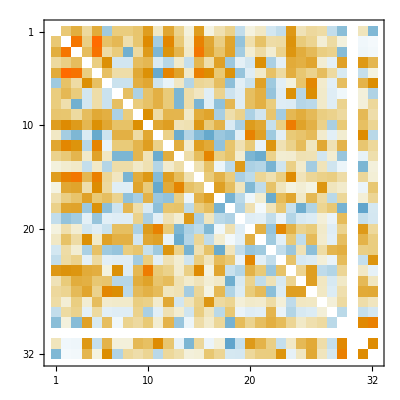

```mathematica
MatrixPlot[binaryCorrMap]
```

```mathematica
binaryCorrMap//Max
```

0.904842

```mathematica
binaryCorrList=Flatten[MapIndexed[f,binaryCorrMap,{2}],1];
```

```mathematica
binaryCorrListSort=Sort[binaryCorrList,#1[[1]]>#2[[1]]&];
```

```mathematica
binaryCorrListSort[[1;;8]]
```

{f[0.904842,{5,2}],f[0.904842,{2,5}],f[0.777778,{5,3}],f[0.777778,{3,5}],f[0.753371,{3,2}],f[0.753371,{2,3}],f[0.714168,{15,3}],f[0.714168,{3,15}]}

交絡 （相関）が強い項目があるはずなので確認。（予想⋆）

(5)「関連度」::(7)「日付」-> 0.78
⋆(5) 「関連度」 :: (20) 「適合性チューニング」-> 0.71
(15)「ビルダー形式GUI」::(30)「V:データプロット」-> 0.65
(7)「日付」::(20)「適合性チューニング」-> 0.58
⋆(14) 「4.ファセット型ナビ」 :: (37)「 N:検索結果リファイン」-> 0.57

```mathematica
headRepRule=Table[{n,n}->1,{n,1,32}]
```

{{1,1}→1,{2,2}→1,{3,3}→1,{4,4}→1,{5,5}→1,{6,6}→1,{7,7}→1,{8,8}→1,{9,9}→1,{10,10}→1,{11,11}→1,{12,12}→1,{13,13}→1,{14,14}→1,{15,15}→1,{16,16}→1,{17,17}→1,{18,18}→1,{19,19}→1,{20,20}→1,{21,21}→1,{22,22}→1,{23,23}→1,{24,24}→1,{25,25}→1,{26,26}→1,{27,27}→1,{28,28}→1,{29,29}→1,{30,30}→1,{31,31}→1,{32,32}→1}

```mathematica
headVecs=ReplacePart[Table[0,{32},{32}],headRepRule];
```

## 除外サイトの除去（採用サイトの決定）

除外対象サイト（除外フラグ）

```mathematica
Map[#[[60]]&,tsvBody]
```

{,1,,1,1,,1,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,1,,,,,,,,,,,,,,}

```mathematica
deleteSite=Position[Map[#[[60]]&,tsvBody],1]
```

{{2},{4},{5},{7},{50}}

採用サイト

```mathematica
(tsvBodySiteD=Delete[tsvBodySite,deleteSite])//Dimensions
```

{59}

採用サイトID

```mathematica
(tsvBodyIDD=Delete[tsvBodyID,deleteSite])//Dimensions
```

{59}

## 採用項目と採用サイトによる行列

```mathematica
(tsvBinaryBodyZDropD=Delete[tsvBinaryBodyZDrop,deleteSite])//Dimensions
```

{59,32}

採用サイトのポイント

```mathematica
Map[Tr,tsvBinaryBodyZDropD]
```

{12,10,13,5,5,14,6,13,13,3,14,17,8,13,9,11,12,12,12,11,10,2,5,14,14,10,10,9,14,9,3,5,18,12,6,4,12,9,13,7,2,9,8,15,4,16,14,18,15,12,4,19,12,6,13,5,9,6,6}

採用項目のポイント

```mathematica
Map[Tr,Transpose[tsvBinaryBodyZDropD]]
```

{14,36,27,2,34,3,4,3,27,25,3,41,55,8,25,47,17,21,1,4,3,11,1,20,5,5,58,1,15,59,12,5}

```mathematica
tsvBodySiteD//Length
```

59

```mathematica
tab59x31=Prepend[Transpose[Prepend[tsvBinaryBodyZDropD,tsvEvalHeadDrop]],Prepend[tsvBodySiteD,"項目"]]
```

{{項目,国民経済計算  :日本:経済・産業統計/報告,科学技術研究調査  :日本:学術統計,科学研究費補助金　配分結果  :日本:補助金情報,科学技術システムの意識定点調査  :日本:経済・産業統計/報告,全国イノベーション調査  :日本:経済・産業統計/報告,J-GLOBAL  :日本:学術総合,researchmap  :日本:学術総合,外国人留学生在籍状況調査  :日本:学生支援,大学ポートレート  :日本:大学情報,大学基本情報  :日本:大学情報,CiNii Articles  :日本:学術論文,KAKEN  :日本:補助金情報,厚生労働科学研究成果データベース  :日本:学術総合,賃金構造基本統計調査  :日本:経済・産業統計/報告,品種登録／出願公表データ  :日本:特許等,経済産業省企業活動基本調査  :日本:経済・産業統計/報告,JIPデータベース  :日本:経済・産業統計/報告,成果報告書データベース  :日本:学術総合,知的財産活動調査  :日本:特許等,特許プラットフォーム  :日本:特許等,IIPパテントデータベース  :日本:特許等,指標情報データベース  :日本:学術総合,Orbis  :世界:経済・産業統計/報告,Main Science and Technology Indicators  :世界:経済・産業統計/報告,Research and Development Statistics  :世界:経済・産業統計/報告,WIPO IP Statistics Data Center  :世界:特許等,World Bank Open Data  :世界:経済・産業統計/報告,Espacenet  :欧州:特許等,Eurostat  :欧州:経済・産業統計/報告,eSearch plus  :欧州:特許等,publicdata.eu  :欧州:医療健康,RISIS Datasets  :欧州:学術総合,Data.gov.uk  :英国:学術総合,Science, engineering and technology Statistics  :英国:学術総合,UNISTATS  :英国:大学情報,Finances of Higher Education Providers  :英国:教育・学校統計/報告,ONS Gross Domestic Expenditure  :英国:経済・産業統計/報告,英国特許庁データベース  :英国:特許等,CWTS Leiden Ranking  :蘭国:学術統計,University-Industry Research Connections  :蘭国:その他,ライデン声明  :蘭国:その他,Bundesbericht Forschung und Innovation  :独国:教育・学校統計/報告,Daten Potal  :独国:教育・学校統計/報告,Förderatlas 2015  :独国:補助金情報,ドイツ特許庁　特許検索データベース  :独国:特許等,Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告,Evaluation Procedures  :仏国:教育・学校統計/報告,data.gouv.fr  :仏国:学術総合,Bases de données gratuites  :仏国:経済・産業統計/報告,Statistiques structurelles  :仏国:経済・産業統計/報告,Repères et références statistiques  :仏国:教育・学校統計/報告,Data.gov  :米国:学術総合,National Bureau of Economic Research  :米国:経済・産業統計/報告,Academic Institution Profiles  :米国:学術総合,WebCASPAR  :米国:学術総合,Science and Engineering Indicators  :米国:学術統計,FedScope-Federal Human Resources Data  :米国:経済・産業統計/報告,米国特許検索データベース  :米国:特許等,サンフランシスコ宣言  :米国:その他},{**サジェスト,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,0,1,0,0,0,0},{2.ベストファースト = O:ソート,1,0,1,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,0,0,0,1,1,0,0,1,1,1,0,0,1,0,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0},{* 関連度,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,1,0,1,1,0,0,0,1,1,0,0,1,1,0,0,0,1,0,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0},{* 人気度,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0},{* 日付,1,0,1,0,0,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,0,0,0,1,1,0,0,1,1,0,0,0,1,0,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0},{* フォーマット（ソースの）,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{**スコア,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{**エンジン（マルチエンジン）,1,1,1,0,0,1,0,1,0,0,1,0,0,1,0,1,1,1,0,1,0,0,0,1,1,0,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,1,0,1,1,0},{4. ファセット型ナビ = ファセット型ナビ,1,0,1,0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,0,1,0,1,1,0,0,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,0,0},{L:ビルダー形式GUI,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{5.詳細検索 = K:詳細検索,1,1,1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,1,1,1,0,0,0,0,1,0,1,0,0},{J:検索box,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{X:login機能,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0},{**適合性のチューニング,0,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,1,1,1,1,1,0,0,1,1,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0},{7.ページネーション = ページネーション,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,0,1,0,1,1,0,1,1,1,1,1,1,1,0,0,0,1,0,1,0,1,1,1,1,1,0,1,1,1,0,1,1,1,1},{Q:全件表示,0,0,0,1,1,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,1,1,0,0,1,1,0,0,0,0,0,1},{**ハイライト,0,0,1,0,0,0,0,1,1,0,1,1,0,1,0,1,0,0,1,0,1,0,0,1,1,1,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1},{**クラスタリング,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{V:データプロット,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{U:マップ,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{S:サムネイル,1,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{W:ロケータ/スライダ等、GUIによる指定,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{N:検索結果リファイン,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0},{**レコメン,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0},{**トピック,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0},{11. NISTEPサービスにあるが本書にない項目（空項目）,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1},{R:バリアフリー,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{P:ダウンロード,0,1,0,0,0,0,0,1,0,1,1,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0},{M:検索対象のタイプ,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{T:ダウンロードのデータ形式,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0},{Z1:API,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}

```mathematica
Directory[]
```

/Volumes/home/NII/基盤_CiNii/研究開発/ディスカバリサービス/NISTEP

```mathematica
Export["NISTEP-DSlink-Target_New-16/tab59x31.tsv",tab59x31]
```

NISTEP-DSlink-Target_New-16/tab59x31.tsv

## 採用サイトの地域・ジャンル(2)

採用サイトの地域

```mathematica
(tsvSiteRegion=Map[StringSplit[#,":"][[2]]&,tsvBodySiteD])//Tally
```

{{日本,22},{世界,5},{欧州,5},{英国,6},{蘭国,3},{独国,5},{仏国,5},{米国,8}}

```mathematica
tsvSiteRegionUnq=Union[tsvSiteRegion]
```

{世界,仏国,日本,欧州,独国,米国,英国,蘭国}

:地域の色の合成

```mathematica
regionColSch=Map[ColorData["BeachColors"][#]&,Range[0,(tsvSiteRegionUnq//Length)-1]/((tsvSiteRegionUnq//Length)-1)]
```

{RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[1., 1., 1.]}

::地域の色のルール

```mathematica
regionColSchRl=Apply[Rule,Transpose[{tsvSiteRegionUnq,regionColSch}],{1}]
```

{世界→RGBColor[0.853407, 0.503288, 0.26041],仏国→RGBColor[0.879024, 0.628064, 0.283622],日本→RGBColor[0.902009, 0.732143, 0.303912],欧州→RGBColor[0.875374, 0.776136, 0.387224],独国→RGBColor[0.799766, 0.761697, 0.551801],米国→RGBColor[0.723459, 0.731524, 0.768181],英国→RGBColor[0.742358, 0.769362, 0.959202],蘭国→RGBColor[1., 1., 1.]}

:::地域の色オブジェクト

```mathematica
regionColObj=(tsvSiteRegion/.regionColSchRl)
```

{RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.742358, 0.769362, 0.959202],RGBColor[1., 1., 1.],RGBColor[1., 1., 1.],RGBColor[1., 1., 1.],RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.723459, 0.731524, 0.768181]}

採用サイトのジャンル

```mathematica
(tsvSiteGenre=Map[StringSplit[#,":"][[3]]&,tsvBodySiteD])//Tally
```

{{経済・産業統計/報告,17},{学術統計,3},{補助金情報,3},{学術総合,12},{学生支援,1},{大学情報,3},{学術論文,1},{特許等,10},{医療健康,1},{教育・学校統計/報告,5},{その他,3}}

```mathematica
tsvSiteGenreUnq=Union[tsvSiteGenre]
```

{その他,特許等,医療健康,大学情報,学生支援,学術統計,学術総合,学術論文,補助金情報,教育・学校統計/報告,経済・産業統計/報告}

:ジャンルの色の合成

```mathematica
genreColSch=Map[ColorData["CMYKColors"][#]&,Range[0,(tsvSiteGenreUnq//Length)-1]/((tsvSiteGenreUnq//Length)-1)]
```

{RGBColor[0.300725, 0.680491, 0.901701],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.604318, 0.51771, 0.780231],RGBColor[0.738903, 0.424989, 0.675772],RGBColor[0.843122, 0.472052, 0.589251],RGBColor[0.9112395, 0.6309425, 0.5195245],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.9153045, 0.849461, 0.511525],RGBColor[0.806801, 0.785304, 0.566474],RGBColor[0.5533805, 0.5446295, 0.49991150000000006],RGBColor[0.133532, 0.122103, 0.125444]}

::ジャンルの色のルール

```mathematica
genreColSchRl=Apply[Rule,Transpose[{tsvSiteGenreUnq,genreColSch}],{1}]
```

{その他→RGBColor[0.300725, 0.680491, 0.901701],特許等→RGBColor[0.4414085, 0.6946559999999999, 0.8996385],医療健康→RGBColor[0.604318, 0.51771, 0.780231],大学情報→RGBColor[0.738903, 0.424989, 0.675772],学生支援→RGBColor[0.843122, 0.472052, 0.589251],学術統計→RGBColor[0.9112395, 0.6309425, 0.5195245],学術総合→RGBColor[0.945344, 0.789625, 0.482689],学術論文→RGBColor[0.9153045, 0.849461, 0.511525],補助金情報→RGBColor[0.806801, 0.785304, 0.566474],教育・学校統計/報告→RGBColor[0.5533805, 0.5446295, 0.49991150000000006],経済・産業統計/報告→RGBColor[0.133532, 0.122103, 0.125444]}

:::ジャンルの色オブジェクト

```mathematica
genreColObj=(tsvSiteGenre/.genreColSchRl)
```

{RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.9112395, 0.6309425, 0.5195245],RGBColor[0.806801, 0.785304, 0.566474],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.843122, 0.472052, 0.589251],RGBColor[0.738903, 0.424989, 0.675772],RGBColor[0.738903, 0.424989, 0.675772],RGBColor[0.9153045, 0.849461, 0.511525],RGBColor[0.806801, 0.785304, 0.566474],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.604318, 0.51771, 0.780231],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.738903, 0.424989, 0.675772],RGBColor[0.5533805, 0.5446295, 0.49991150000000006],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.9112395, 0.6309425, 0.5195245],RGBColor[0.300725, 0.680491, 0.901701],RGBColor[0.300725, 0.680491, 0.901701],RGBColor[0.5533805, 0.5446295, 0.49991150000000006],RGBColor[0.5533805, 0.5446295, 0.49991150000000006],RGBColor[0.806801, 0.785304, 0.566474],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.5533805, 0.5446295, 0.49991150000000006],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.5533805, 0.5446295, 0.49991150000000006],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.945344, 0.789625, 0.482689],RGBColor[0.9112395, 0.6309425, 0.5195245],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.4414085, 0.6946559999999999, 0.8996385],RGBColor[0.300725, 0.680491, 0.901701]}

```mathematica
tsvBodySiteDC=Transpose[{tsvBodySiteD,regionColObj,genreColObj}]
```

{{国民経済計算  :日本:経済・産業統計/報告,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.133532, 0.122103, 0.125444]},{科学技術研究調査  :日本:学術統計,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.9112395, 0.6309425, 0.5195245]},{科学研究費補助金　配分結果  :日本:補助金情報,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.806801, 0.785304, 0.566474]},{科学技術システムの意識定点調査  :日本:経済・産業統計/報告,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.133532, 0.122103, 0.125444]},{全国イノベーション調査  :日本:経済・産業統計/報告,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.133532, 0.122103, 0.125444]},{J-GLOBAL  :日本:学術総合,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.945344, 0.789625, 0.482689]},{researchmap  :日本:学術総合,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.945344, 0.789625, 0.482689]},{外国人留学生在籍状況調査  :日本:学生支援,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.843122, 0.472052, 0.589251]},{大学ポートレート  :日本:大学情報,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.738903, 0.424989, 0.675772]},{大学基本情報  :日本:大学情報,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.738903, 0.424989, 0.675772]},{CiNii Articles  :日本:学術論文,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.9153045, 0.849461, 0.511525]},{KAKEN  :日本:補助金情報,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.806801, 0.785304, 0.566474]},{厚生労働科学研究成果データベース  :日本:学術総合,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.945344, 0.789625, 0.482689]},{賃金構造基本統計調査  :日本:経済・産業統計/報告,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.133532, 0.122103, 0.125444]},{品種登録／出願公表データ  :日本:特許等,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{経済産業省企業活動基本調査  :日本:経済・産業統計/報告,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.133532, 0.122103, 0.125444]},{JIPデータベース  :日本:経済・産業統計/報告,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.133532, 0.122103, 0.125444]},{成果報告書データベース  :日本:学術総合,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.945344, 0.789625, 0.482689]},{知的財産活動調査  :日本:特許等,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{特許プラットフォーム  :日本:特許等,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{IIPパテントデータベース  :日本:特許等,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{指標情報データベース  :日本:学術総合,RGBColor[0.902009, 0.732143, 0.303912],RGBColor[0.945344, 0.789625, 0.482689]},{Orbis  :世界:経済・産業統計/報告,RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.133532, 0.122103, 0.125444]},{Main Science and Technology Indicators  :世界:経済・産業統計/報告,RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.133532, 0.122103, 0.125444]},{Research and Development Statistics  :世界:経済・産業統計/報告,RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.133532, 0.122103, 0.125444]},{WIPO IP Statistics Data Center  :世界:特許等,RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{World Bank Open Data  :世界:経済・産業統計/報告,RGBColor[0.853407, 0.503288, 0.26041],RGBColor[0.133532, 0.122103, 0.125444]},{Espacenet  :欧州:特許等,RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{Eurostat  :欧州:経済・産業統計/報告,RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.133532, 0.122103, 0.125444]},{eSearch plus  :欧州:特許等,RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{publicdata.eu  :欧州:医療健康,RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.604318, 0.51771, 0.780231]},{RISIS Datasets  :欧州:学術総合,RGBColor[0.875374, 0.776136, 0.387224],RGBColor[0.945344, 0.789625, 0.482689]},{Data.gov.uk  :英国:学術総合,RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.945344, 0.789625, 0.482689]},{Science, engineering and technology Statistics  :英国:学術総合,RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.945344, 0.789625, 0.482689]},{UNISTATS  :英国:大学情報,RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.738903, 0.424989, 0.675772]},{Finances of Higher Education Providers  :英国:教育・学校統計/報告,RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.5533805, 0.5446295, 0.49991150000000006]},{ONS Gross Domestic Expenditure  :英国:経済・産業統計/報告,RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.133532, 0.122103, 0.125444]},{英国特許庁データベース  :英国:特許等,RGBColor[0.742358, 0.769362, 0.959202],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{CWTS Leiden Ranking  :蘭国:学術統計,RGBColor[1., 1., 1.],RGBColor[0.9112395, 0.6309425, 0.5195245]},{University-Industry Research Connections  :蘭国:その他,RGBColor[1., 1., 1.],RGBColor[0.300725, 0.680491, 0.901701]},{ライデン声明  :蘭国:その他,RGBColor[1., 1., 1.],RGBColor[0.300725, 0.680491, 0.901701]},{Bundesbericht Forschung und Innovation  :独国:教育・学校統計/報告,RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.5533805, 0.5446295, 0.49991150000000006]},{Daten Potal  :独国:教育・学校統計/報告,RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.5533805, 0.5446295, 0.49991150000000006]},{Förderatlas 2015  :独国:補助金情報,RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.806801, 0.785304, 0.566474]},{ドイツ特許庁　特許検索データベース  :独国:特許等,RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告,RGBColor[0.799766, 0.761697, 0.551801],RGBColor[0.133532, 0.122103, 0.125444]},{Evaluation Procedures  :仏国:教育・学校統計/報告,RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.5533805, 0.5446295, 0.49991150000000006]},{data.gouv.fr  :仏国:学術総合,RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.945344, 0.789625, 0.482689]},{Bases de données gratuites  :仏国:経済・産業統計/報告,RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.133532, 0.122103, 0.125444]},{Statistiques structurelles  :仏国:経済・産業統計/報告,RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.133532, 0.122103, 0.125444]},{Repères et références statistiques  :仏国:教育・学校統計/報告,RGBColor[0.879024, 0.628064, 0.283622],RGBColor[0.5533805, 0.5446295, 0.49991150000000006]},{Data.gov  :米国:学術総合,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.945344, 0.789625, 0.482689]},{National Bureau of Economic Research  :米国:経済・産業統計/報告,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.133532, 0.122103, 0.125444]},{Academic Institution Profiles  :米国:学術総合,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.945344, 0.789625, 0.482689]},{WebCASPAR  :米国:学術総合,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.945344, 0.789625, 0.482689]},{Science and Engineering Indicators  :米国:学術統計,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.9112395, 0.6309425, 0.5195245]},{FedScope-Federal Human Resources Data  :米国:経済・産業統計/報告,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.133532, 0.122103, 0.125444]},{米国特許検索データベース  :米国:特許等,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.4414085, 0.6946559999999999, 0.8996385]},{サンフランシスコ宣言  :米国:その他,RGBColor[0.723459, 0.731524, 0.768181],RGBColor[0.300725, 0.680491, 0.901701]}}

## 採用サイトの地域・ジャンル(3)

採用サイトの地域

```mathematica
(tsvSiteRegion=Map[StringSplit[#,":"][[2]]&,tsvBodySiteD])//Tally
```

{{日本,22},{世界,5},{欧州,5},{英国,6},{蘭国,3},{独国,5},{仏国,5},{米国,8}}

```mathematica
tsvSiteRegionUnq=Union[tsvSiteRegion]
```

{世界,仏国,日本,欧州,独国,米国,英国,蘭国}

:地域のマーク

```mathematica
regionMark={"○","●","◎","◉","△","▲","□","■"}
```

{○,●,◎,◉,△,▲,□,■}

::地域のマークのルール

```mathematica
regionMarkRl=Inner[Rule,tsvSiteRegionUnq,regionMark,List]
```

{世界→○,仏国→●,日本→◎,欧州→◉,独国→△,米国→▲,英国→□,蘭国→■}

::: 地域のマークオブジェクト

```mathematica
regionMkObj=(tsvSiteRegion/.regionMarkRl)
```

{◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,◎,○,○,○,○,○,◉,◉,◉,◉,◉,□,□,□,□,□,□,■,■,■,△,△,△,△,△,●,●,●,●,●,▲,▲,▲,▲,▲,▲,▲,▲}

採用サイトのジャンル

```mathematica
(tsvSiteGenre=Map[StringSplit[#,":"][[3]]&,tsvBodySiteD])//Tally
```

{{経済・産業統計/報告,17},{学術統計,3},{補助金情報,3},{学術総合,12},{学生支援,1},{大学情報,3},{学術論文,1},{特許等,10},{医療健康,1},{教育・学校統計/報告,5},{その他,3}}

```mathematica
tsvSiteGenreUnq=Union[tsvSiteGenre]
```

{その他,特許等,医療健康,大学情報,学生支援,学術統計,学術総合,学術論文,補助金情報,教育・学校統計/報告,経済・産業統計/報告}

::ジャンルのマークのルール

```mathematica
genreMarkRl={"その他"->"x","特許等"->"●","医療健康"->"○","大学情報"->"◎","学生支援"->"◉","学術統計"->"△","学術総合"->"▲","学術論文"->"■","補助金情報"->"□","教育・学校統計/報告"->"◇","経済・産業統計/報告"->"◆"}
```

{その他→x,特許等→●,医療健康→○,大学情報→◎,学生支援→◉,学術統計→△,学術総合→▲,学術論文→■,補助金情報→□,教育・学校統計/報告→◇,経済・産業統計/報告→◆}

:::ジャンルのマークオブジェクト

```mathematica
genreMkObj=(tsvSiteGenre/.genreMarkRl)
```

{◆,△,□,◆,◆,▲,▲,◉,◎,◎,■,□,▲,◆,●,◆,◆,▲,●,●,●,▲,◆,◆,◆,●,◆,●,◆,●,○,▲,▲,▲,◎,◇,◆,●,△,x,x,◇,◇,□,●,◆,◇,▲,◆,◆,◇,▲,◆,▲,▲,△,◆,●,x}

```mathematica
tsvBodySiteDM=Transpose[{tsvBodySiteD,regionMkObj,genreMkObj}]
```

{{国民経済計算  :日本:経済・産業統計/報告,◎,◆},{科学技術研究調査  :日本:学術統計,◎,△},{科学研究費補助金　配分結果  :日本:補助金情報,◎,□},{科学技術システムの意識定点調査  :日本:経済・産業統計/報告,◎,◆},{全国イノベーション調査  :日本:経済・産業統計/報告,◎,◆},{J-GLOBAL  :日本:学術総合,◎,▲},{researchmap  :日本:学術総合,◎,▲},{外国人留学生在籍状況調査  :日本:学生支援,◎,◉},{大学ポートレート  :日本:大学情報,◎,◎},{大学基本情報  :日本:大学情報,◎,◎},{CiNii Articles  :日本:学術論文,◎,■},{KAKEN  :日本:補助金情報,◎,□},{厚生労働科学研究成果データベース  :日本:学術総合,◎,▲},{賃金構造基本統計調査  :日本:経済・産業統計/報告,◎,◆},{品種登録／出願公表データ  :日本:特許等,◎,●},{経済産業省企業活動基本調査  :日本:経済・産業統計/報告,◎,◆},{JIPデータベース  :日本:経済・産業統計/報告,◎,◆},{成果報告書データベース  :日本:学術総合,◎,▲},{知的財産活動調査  :日本:特許等,◎,●},{特許プラットフォーム  :日本:特許等,◎,●},{IIPパテントデータベース  :日本:特許等,◎,●},{指標情報データベース  :日本:学術総合,◎,▲},{Orbis  :世界:経済・産業統計/報告,○,◆},{Main Science and Technology Indicators  :世界:経済・産業統計/報告,○,◆},{Research and Development Statistics  :世界:経済・産業統計/報告,○,◆},{WIPO IP Statistics Data Center  :世界:特許等,○,●},{World Bank Open Data  :世界:経済・産業統計/報告,○,◆},{Espacenet  :欧州:特許等,◉,●},{Eurostat  :欧州:経済・産業統計/報告,◉,◆},{eSearch plus  :欧州:特許等,◉,●},{publicdata.eu  :欧州:医療健康,◉,○},{RISIS Datasets  :欧州:学術総合,◉,▲},{Data.gov.uk  :英国:学術総合,□,▲},{Science, engineering and technology Statistics  :英国:学術総合,□,▲},{UNISTATS  :英国:大学情報,□,◎},{Finances of Higher Education Providers  :英国:教育・学校統計/報告,□,◇},{ONS Gross Domestic Expenditure  :英国:経済・産業統計/報告,□,◆},{英国特許庁データベース  :英国:特許等,□,●},{CWTS Leiden Ranking  :蘭国:学術統計,■,△},{University-Industry Research Connections  :蘭国:その他,■,x},{ライデン声明  :蘭国:その他,■,x},{Bundesbericht Forschung und Innovation  :独国:教育・学校統計/報告,△,◇},{Daten Potal  :独国:教育・学校統計/報告,△,◇},{Förderatlas 2015  :独国:補助金情報,△,□},{ドイツ特許庁　特許検索データベース  :独国:特許等,△,●},{Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告,△,◆},{Evaluation Procedures  :仏国:教育・学校統計/報告,●,◇},{data.gouv.fr  :仏国:学術総合,●,▲},{Bases de données gratuites  :仏国:経済・産業統計/報告,●,◆},{Statistiques structurelles  :仏国:経済・産業統計/報告,●,◆},{Repères et références statistiques  :仏国:教育・学校統計/報告,●,◇},{Data.gov  :米国:学術総合,▲,▲},{National Bureau of Economic Research  :米国:経済・産業統計/報告,▲,◆},{Academic Institution Profiles  :米国:学術総合,▲,▲},{WebCASPAR  :米国:学術総合,▲,▲},{Science and Engineering Indicators  :米国:学術統計,▲,△},{FedScope-Federal Human Resources Data  :米国:経済・産業統計/報告,▲,◆},{米国特許検索データベース  :米国:特許等,▲,●},{サンフランシスコ宣言  :米国:その他,▲,x}}

## サービス項目数トップ

```mathematica
siteScore=Map[Tr,tsvBinaryBodyZDropD]
```

{12,10,13,5,5,14,6,13,13,3,14,17,8,13,9,11,12,12,12,11,10,2,5,14,14,10,10,9,14,9,3,5,18,12,6,4,12,9,13,7,2,9,8,15,4,16,14,18,15,12,4,19,12,6,13,5,9,6,6}

サイトのスコア

```mathematica
siteScoreTop=Sort[({tsvBodyIDD,tsvBodySiteD,siteScore}//Transpose),#1[[3]]>#2[[3]]&]
```

{{90,Data.gov  :米国:学術総合,19},{83,data.gouv.fr  :仏国:学術総合,18},{61,Data.gov.uk  :英国:学術総合,18},{24,KAKEN  :日本:補助金情報,17},{77,Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告,16},{84,Bases de données gratuites  :仏国:経済・産業統計/報告,15},{73,Förderatlas 2015  :独国:補助金情報,15},{82,Evaluation Procedures  :仏国:教育・学校統計/報告,14},{57,Eurostat  :欧州:経済・産業統計/報告,14},{48,Research and Development Statistics  :世界:経済・産業統計/報告,14},{46,Main Science and Technology Indicators  :世界:経済・産業統計/報告,14},{23,CiNii Articles  :日本:学術論文,14},{18,J-GLOBAL  :日本:学術総合,14},{103,WebCASPAR  :米国:学術総合,13},{68,CWTS Leiden Ranking  :蘭国:学術統計,13},{26,賃金構造基本統計調査  :日本:経済・産業統計/報告,13},{21,大学ポートレート  :日本:大学情報,13},{20,外国人留学生在籍状況調査  :日本:学生支援,13},{7,科学研究費補助金　配分結果  :日本:補助金情報,13},{91,National Bureau of Economic Research  :米国:経済・産業統計/報告,12},{85,Statistiques structurelles  :仏国:経済・産業統計/報告,12},{66,ONS Gross Domestic Expenditure  :英国:経済・産業統計/報告,12},{62,Science, engineering and technology Statistics  :英国:学術総合,12},{36,知的財産活動調査  :日本:特許等,12},{35,成果報告書データベース  :日本:学術総合,12},{32,JIPデータベース  :日本:経済・産業統計/報告,12},{1,国民経済計算  :日本:経済・産業統計/報告,12},{37,特許プラットフォーム  :日本:特許等,11},{28,経済産業省企業活動基本調査  :日本:経済・産業統計/報告,11},{54,World Bank Open Data  :世界:経済・産業統計/報告,10},{53,WIPO IP Statistics Data Center  :世界:特許等,10},{38,IIPパテントデータベース  :日本:特許等,10},{4,科学技術研究調査  :日本:学術統計,10},{105,FedScope-Federal Human Resources Data  :米国:経済・産業統計/報告,9},{71,Bundesbericht Forschung und Innovation  :独国:教育・学校統計/報告,9},{67,英国特許庁データベース  :英国:特許等,9},{58,eSearch plus  :欧州:特許等,9},{55,Espacenet  :欧州:特許等,9},{27,品種登録／出願公表データ  :日本:特許等,9},{72,Daten Potal  :独国:教育・学校統計/報告,8},{25,厚生労働科学研究成果データベース  :日本:学術総合,8},{69,University-Industry Research Connections  :蘭国:その他,7},{108,サンフランシスコ宣言  :米国:その他,6},{106,米国特許検索データベース  :米国:特許等,6},{93,Academic Institution Profiles  :米国:学術総合,6},{63,UNISTATS  :英国:大学情報,6},{19,researchmap  :日本:学術総合,6},{104,Science and Engineering Indicators  :米国:学術統計,5},{60,RISIS Datasets  :欧州:学術総合,5},{43,Orbis  :世界:経済・産業統計/報告,5},{16,全国イノベーション調査  :日本:経済・産業統計/報告,5},{15,科学技術システムの意識定点調査  :日本:経済・産業統計/報告,5},{86,Repères et références statistiques  :仏国:教育・学校統計/報告,4},{74,ドイツ特許庁　特許検索データベース  :独国:特許等,4},{64,Finances of Higher Education Providers  :英国:教育・学校統計/報告,4},{59,publicdata.eu  :欧州:医療健康,3},{22,大学基本情報  :日本:大学情報,3},{70,ライデン声明  :蘭国:その他,2},{42,指標情報データベース  :日本:学術総合,2}}

```mathematica
siteScoreTop[[1;;5]]//TableForm
```

90 | Data.gov  :米国:学術総合 | 19
83 | data.gouv.fr  :仏国:学術総合 | 18
61 | Data.gov.uk  :英国:学術総合 | 18
24 | KAKEN  :日本:補助金情報 | 17
77 | Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告 | 16

```mathematica
siteScoreTop//TableForm
```

90 | Data.gov  :米国:学術総合 | 19
83 | data.gouv.fr  :仏国:学術総合 | 18
61 | Data.gov.uk  :英国:学術総合 | 18
24 | KAKEN  :日本:補助金情報 | 17
77 | Ausgaben, Einnahmen und Personal  :独国:経済・産業統計/報告 | 16
84 | Bases de données gratuites  :仏国:経済・産業統計/報告 | 15
73 | Förderatlas 2015  :独国:補助金情報 | 15
82 | Evaluation Procedures  :仏国:教育・学校統計/報告 | 14
57 | Eurostat  :欧州:経済・産業統計/報告 | 14
48 | Research and Development Statistics  :世界:経済・産業統計/報告 | 14
46 | Main Science and Technology Indicators  :世界:経済・産業統計/報告 | 14
23 | CiNii Articles  :日本:学術論文 | 14
18 | J-GLOBAL  :日本:学術総合 | 14
103 | WebCASPAR  :米国:学術総合 | 13
68 | CWTS Leiden Ranking  :蘭国:学術統計 | 13
26 | 賃金構造基本統計調査  :日本:経済・産業統計/報告 | 13
21 | 大学ポートレート  :日本:大学情報 | 13
20 | 外国人留学生在籍状況調査  :日本:学生支援 | 13
7 | 科学研究費補助金　配分結果  :日本:補助金情報 | 13
91 | National Bureau of Economic Research  :米国:経済・産業統計/報告 | 12
85 | Statistiques structurelles  :仏国:経済・産業統計/報告 | 12
66 | ONS Gross Domestic Expenditure  :英国:経済・産業統計/報告 | 12
62 | Science, engineering and technology Statistics  :英国:学術総合 | 12
36 | 知的財産活動調査  :日本:特許等 | 12
35 | 成果報告書データベース  :日本:学術総合 | 12
32 | JIPデータベース  :日本:経済・産業統計/報告 | 12
1 | 国民経済計算  :日本:経済・産業統計/報告 | 12
37 | 特許プラットフォーム  :日本:特許等 | 11
28 | 経済産業省企業活動基本調査  :日本:経済・産業統計/報告 | 11
54 | World Bank Open Data  :世界:経済・産業統計/報告 | 10
53 | WIPO IP Statistics Data Center  :世界:特許等 | 10
38 | IIPパテントデータベース  :日本:特許等 | 10
4 | 科学技術研究調査  :日本:学術統計 | 10
105 | FedScope-Federal Human Resources Data  :米国:経済・産業統計/報告 | 9
71 | Bundesbericht Forschung und Innovation  :独国:教育・学校統計/報告 | 9
67 | 英国特許庁データベース  :英国:特許等 | 9
58 | eSearch plus  :欧州:特許等 | 9
55 | Espacenet  :欧州:特許等 | 9
27 | 品種登録／出願公表データ  :日本:特許等 | 9
72 | Daten Potal  :独国:教育・学校統計/報告 | 8
25 | 厚生労働科学研究成果データベース  :日本:学術総合 | 8
69 | University-Industry Research Connections  :蘭国:その他 | 7
108 | サンフランシスコ宣言  :米国:その他 | 6
106 | 米国特許検索データベース  :米国:特許等 | 6
93 | Academic Institution Profiles  :米国:学術総合 | 6
63 | UNISTATS  :英国:大学情報 | 6
19 | researchmap  :日本:学術総合 | 6
104 | Science and Engineering Indicators  :米国:学術統計 | 5
60 | RISIS Datasets  :欧州:学術総合 | 5
43 | Orbis  :世界:経済・産業統計/報告 | 5
16 | 全国イノベーション調査  :日本:経済・産業統計/報告 | 5
15 | 科学技術システムの意識定点調査  :日本:経済・産業統計/報告 | 5
86 | Repères et références statistiques  :仏国:教育・学校統計/報告 | 4
74 | ドイツ特許庁　特許検索データベース  :独国:特許等 | 4
64 | Finances of Higher Education Providers  :英国:教育・学校統計/報告 | 4
59 | publicdata.eu  :欧州:医療健康 | 3
22 | 大学基本情報  :日本:大学情報 | 3
70 | ライデン声明  :蘭国:その他 | 2
42 | 指標情報データベース  :日本:学術総合 | 2

```mathematica
Map[#[[1]]&,siteScoreTop[[1;;5]]]
```

{90,83,61,24,77}

```mathematica
siteScoreTopPos=Map[Position[tsvBodyIDD,#[[1]]][[1]]&,siteScoreTop[[1;;5]]]
```

{{52},{48},{33},{12},{46}}

Top4で違いのある項目

```mathematica
siteScoreTopVec=tsvBinaryBodyZDropD[[Flatten[siteScoreTopPos]]]
```

{{0,1,1,1,1,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,1,0,0,1,0,1,1,0,1,1,1,1},{1,1,1,1,1,0,0,0,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,1,0,1,0,1,1,1,0},{0,1,1,0,1,1,0,0,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1},{0,1,1,0,1,0,0,0,0,1,0,1,1,0,1,1,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1},{1,1,1,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,0,1,1,0,0,1,0,0}}

```mathematica
Count[Map[Tr,Transpose[siteScoreTopVec]],x_/;x>0&&x<4]
```

12

```mathematica
{Range[32],tsvEvalHeadDrop,Map[Tr,Transpose[siteScoreTopVec]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32
**サジェスト | 2.ベストファースト = O:ソート | * 関連度 | * 人気度 | * 日付 | * フォーマット（ソースの） | * 多様性（多様性(表現の多様性の吸収など)アルゴリズム） | **スコア | **エンジン（マルチエンジン） | 4. ファセット型ナビ = ファセット型ナビ | L:ビルダー形式GUI | 5.詳細検索 = K:詳細検索 | J:検索box | X:login機能 | **適合性のチューニング | 7.ページネーション = ページネーション | Q:全件表示 | **ハイライト | **クラスタリング | V:データプロット | U:マップ | S:サムネイル | W:ロケータ/スライダ等、GUIによる指定 | N:検索結果リファイン | **レコメン | **トピック | 11. NISTEPサービスにあるが本書にない項目（空項目） | R:バリアフリー | P:ダウンロード | M:検索対象のタイプ | T:ダウンロードのデータ形式 | Z1:API
2 | 5 | 5 | 2 | 5 | 2 | 1 | 0 | 4 | 5 | 0 | 4 | 5 | 0 | 5 | 5 | 5 | 1 | 0 | 1 | 1 | 0 | 1 | 4 | 2 | 3 | 5 | 0 | 4 | 5 | 3 | 3

## 稀な項目

```mathematica
(hitCount=Map[Tr,tsvBinaryBodyZDropD//Transpose])
```

{14,36,27,2,34,3,4,3,27,25,3,41,55,8,25,47,17,21,1,4,3,11,1,20,5,5,58,1,15,59,12,5}

```mathematica
Position[hitCount,1]
```

{{19},{23},{28}}

```mathematica
hitCountTop=Sort[{hitCount,tsvEvalHeadDrop}//Transpose,#1[[1]]<#2[[1]]&]
```

{{1,R:バリアフリー},{1,W:ロケータ/スライダ等、GUIによる指定},{1,**クラスタリング},{2,* 人気度},{3,U:マップ},{3,L:ビルダー形式GUI},{3,**スコア},{3,* フォーマット（ソースの）},{4,V:データプロット},{4,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）},{5,Z1:API},{5,**トピック},{5,**レコメン},{8,X:login機能},{11,S:サムネイル},{12,T:ダウンロードのデータ形式},{14,**サジェスト},{15,P:ダウンロード},{17,Q:全件表示},{20,N:検索結果リファイン},{21,**ハイライト},{25,**適合性のチューニング},{25,4. ファセット型ナビ = ファセット型ナビ},{27,**エンジン（マルチエンジン）},{27,* 関連度},{34,* 日付},{36,2.ベストファースト = O:ソート},{41,5.詳細検索 = K:詳細検索},{47,7.ページネーション = ページネーション},{55,J:検索box},{58,11. NISTEPサービスにあるが本書にない項目（空項目）},{59,M:検索対象のタイプ}}

```mathematica
hitCountTop[[1;;3]]//TableForm
```

1 | R:バリアフリー
1 | W:ロケータ/スライダ等、GUIによる指定
1 | **クラスタリング

## 階層クラスタリング(パッケージロード)

```mathematica
Needs["HierarchicalClustering`"]
```

## 階層クラスタリング(2)

```mathematica
tsvBodySiteD//Dimensions
```

{59}

```mathematica
tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}]}]&,tsvBodySiteD];
```

```mathematica
tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}],Point[{0,1.3}]}]&,tsvBodySiteD];
```

```mathematica
tx=Map[Graphics[{PointSize[0.05],Text[Style[#[[1]],6],{0,0},{0,0},{0,-1}],#[[2]],Point[{0,1.7}],#[[3]],Point[{0,1.6}]}]&,tsvBodySiteDC];
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

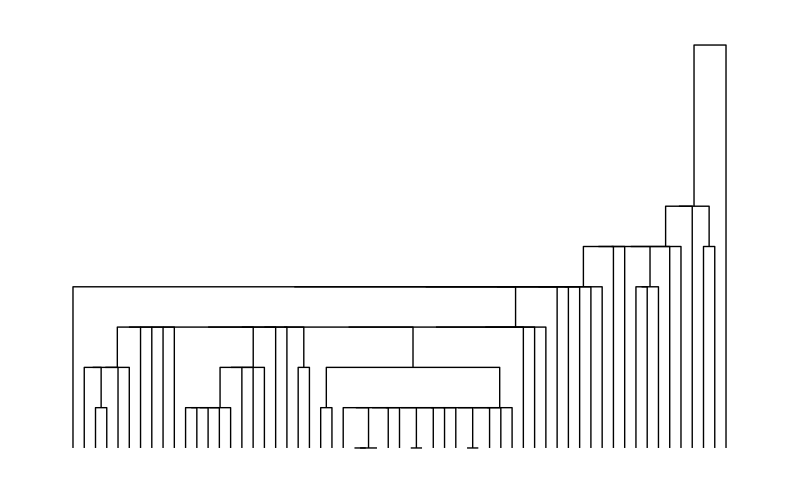
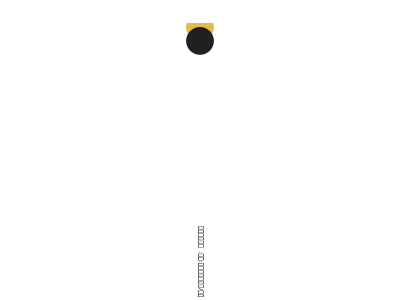
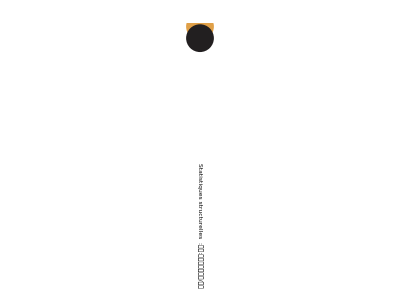
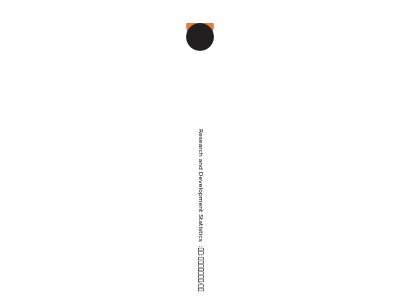
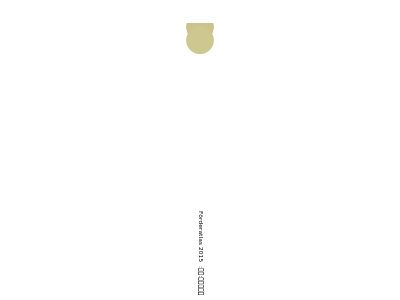
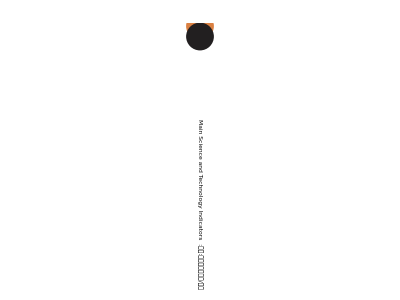
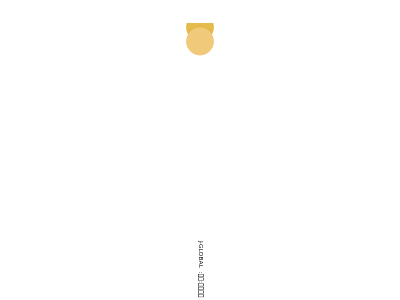
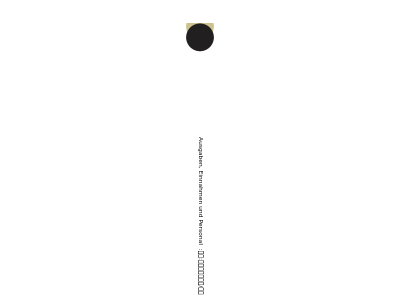

```mathematica
dp=DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx]
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

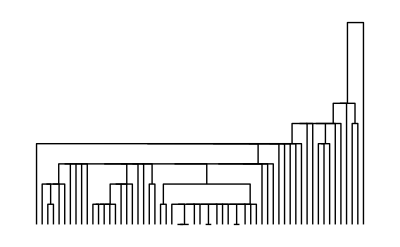
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx,DistanceFunction->SquaredEuclideanDistance]
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

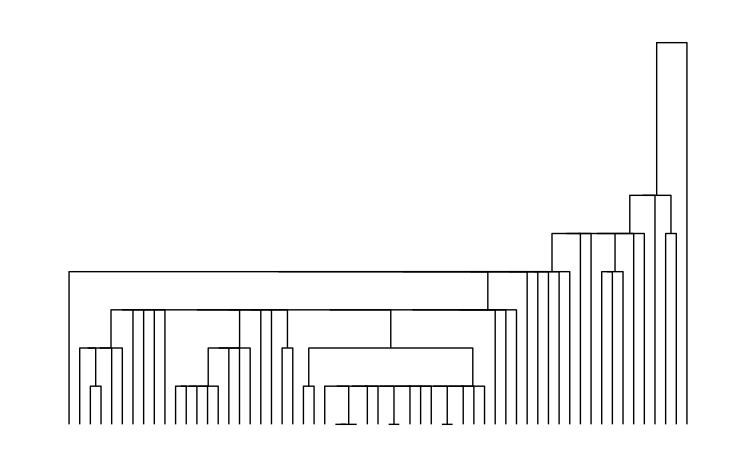
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx,DistanceFunction->SquaredEuclideanDistance,Linkage->"Single"]
```

## 階層クラスタリング(4)

```mathematica
tsvBodySiteD//Dimensions
```

{59}

```mathematica
(*tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}]}]&,tsvBodySiteD];*)
```

```mathematica
(*tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}]}]&,tsvBodySiteD]*)
```

```mathematica
(*tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}],Point[{0,1.3}]}]&,tsvBodySiteD];*)
```

```mathematica
tx=Map[Graphics[{Text[Style[#[[1]],6],{0,-0.13},{0,0},{0,-1}],Text[Style[#[[2]],8],{0,1.1},{0,0},{0,-1}],Text[Style[#[[3]],8],{0,1},{0,0},{0,-1}]}]&,tsvBodySiteDM];
```

```mathematica
dp=DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx]
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

-Graphics-

```mathematica
DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx,DistanceFunction->SquaredEuclideanDistance]
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

-Graphics-

```mathematica
DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx,DistanceFunction->EuclideanDistance,Linkage->"Single"]
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

-Graphics-

## サービスの空間配置の確認(PCA)

### 規格化なし；分散法

```mathematica
(pca=PrincipalComponents[N[tsvBinaryBodyZDropD]])//Dimensions
```

{59,32}

クラスタリング用データのExport

```mathematica
Export["zeroDrop_.sv",matTokmeansSV[tsvBinaryBodyZDropD],"Text"]
```

zeroDrop_.sv

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,pca]},Frame->True,PlotLabel->"規格化なし"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,pca]}]
```

-Graphics3D-

### 規格化なし；相関法*

```mathematica
(pcaC=PrincipalComponents[N[tsvBinaryBodyZDropD],Method->"Correlation"])//Dimensions
```

{59,32}

```mathematica
(txpos=Map[#[[Range[2]]]&,pcaC])//Length
```

59

```mathematica
(txPCA=tsvBodySiteD)//Length
```

59

```mathematica
gtxt=Table[Text[txPCA[[n]],txpos[[n]]+{0,-0.13}],{n,Length[txPCA]}];
```

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,pcaC],gtxt},Frame->True,PlotLabel->"規格化なし、相関法"]
```

-Graphics-

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,pcaC]},Frame->True,PlotLabel->"規格化なし、相関法"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,pcaC]}]
```

-Graphics3D-

### カウント規格化；分散法

```mathematica
(cnpca=PrincipalComponents[tsvBinaryBodyZDropDCN=Transpose[Map[countNormal,Transpose[N[tsvBinaryBodyZDropD]]]]])//Dimensions
```

{59,32}

クラスタリング用データのExport

```mathematica
Export["zeroDrop_CN.sv",matTokmeansSV[tsvBinaryBodyZDropDCN],"Text"]
```

zeroDrop_CN.sv

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,cnpca]},Frame->True, PlotLabel->"カウント規格化"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,cnpca]}]
```

-Graphics3D-

### カウント規格化；相関法

```mathematica
(cnpcaC=PrincipalComponents[Transpose[Map[countNormal,Transpose[N[tsvBinaryBodyZDropD]]]],Method->"Correlation"])//Dimensions
```

{59,32}

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,cnpcaC]},Frame->True,PlotLabel->"カウント規格化、相関法"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,cnpcaC]}]
```

-Graphics3D-

### ノルム規格化；分散法

```mathematica
(npca=PrincipalComponents[tsvBinaryBodyZDropDNN=Transpose[Map[Normalize,Transpose[N[tsvBinaryBodyZDropD]]]]])//Dimensions
```

{59,32}

クラスタリング用データのExport

```mathematica
Export["zeroDrop_NN.sv",matTokmeansSV[tsvBinaryBodyZDropDNN],"Text"]
```

zeroDrop_NN.sv

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,npca]},Frame->True,PlotLabel->"ノルム規格化"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,npca]}]
```

-Graphics3D-

### ノルム規格化；相関法

```mathematica
(npcaC=PrincipalComponents[Transpose[Map[Normalize,Transpose[N[tsvBinaryBodyZDropD]]]],Method->"Correlation"])//Dimensions
```

{59,32}

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,npcaC]},Frame->True,PlotLabel->"ノルム規格化、相関法"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,npcaC]}]
```

-Graphics3D-

## サービスの空間配置の確認(LLE)

### 規格化なし

```mathematica
(lle2D=DimensionReduce[N[tsvBinaryBodyZDropD],2,Method->"LLE"])//Dimensions
```

{59,2}

```mathematica
(lle3D=DimensionReduce[N[tsvBinaryBodyZDropD],3,Method->"LLE"])//Dimensions
```

{59,3}

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,lle2D]},Frame->True,PlotLabel->"規格化なし"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,lle3D]}]
```

-Graphics3D-

## 項目空間にマップしたサービスの分布

### 規格化なし；PCA:相関法

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

91

```mathematica
Dimensions[jointBinary=Join[headVecs,tsvBinaryBodyZDropD]]
```

{91,32}

```mathematica
JBPCA=PrincipalComponents[jointBinary//N,Method->"Correlation"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBPCA])//Length
```

91

```mathematica
txPCA=name;
```

```mathematica
gtxt=Table[Text[txPCA[[n]],txpos[[n]]+{0,-0.13}],{n,Length[txPCA]}];
```

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBPCA],gtxt},Frame->True,PlotLabel->"規格化なし、相関法"]
```

-Graphics-

### ノルム規格化；PCA相関法

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

91

```mathematica
Dimensions[jointBinary=Join[headVecs,Map[Normalize,tsvBinaryBodyZDropD]]]
```

{91,32}

```mathematica
JBPCA=PrincipalComponents[jointBinary//N,Method->"Correlation"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBPCA])//Length
```

91

```mathematica
txPCA=name;
```

```mathematica
gtxt=Table[Text[txPCA[[n]],txpos[[n]]+{0,-0.13}],{n,Length[txPCA]}];
```

```mathematica
attPlot["PCA:Norm"]=Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBPCA],gtxt},Frame->True,PlotLabel->"規格化、PCA相関法",ImageSize->{1300,1100}]
```

-Graphics-

```mathematica
Export["AttPlot-PCA_norm.png",attPlot["PCA:Norm"]]
```

AttPlot-PCA_norm.png

### ノルム規格化；MDS

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

91

```mathematica
Dimensions[jointBinary=Join[headVecs,Map[Normalize,tsvBinaryBodyZDropD]]]
```

{91,32}

```mathematica
JBMDS=DimensionReduce[jointBinary//N,2,Method->"MultidimensionalScaling"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBMDS])//Length
```

91

```mathematica
txMDS=name;
```

```mathematica
gtxt=Table[Text[txMDS[[n]],txpos[[n]]+{0,-0.03}],{n,Length[txMDS]}];
```

```mathematica
attPlot["MDS:Norm"]=Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBMDS],gtxt},Frame->True,PlotLabel->"規格化、MDS",ImageSize->{1300,1100}]
```

-Graphics-

```mathematica
Export["AttPlot-MDS_norm.png",attPlot["MDS:Norm"]]
```

AttPlot-MDS_norm.png

### ノルム規格化；TSNE

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

91

```mathematica
Dimensions[jointBinary=Join[headVecs,Map[Normalize,tsvBinaryBodyZDropD]]]
```

{91,32}

```mathematica
JBTSNE=DimensionReduce[jointBinary//N,2,Method->"TSNE"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBTSNE])//Length
```

91

```mathematica
txTSNE=name;
```

```mathematica
gtxt=Table[Text[txTSNE[[n]],txpos[[n]]+{0,-0.16}],{n,Length[txTSNE]}];
```

```mathematica
attPlot["TSNE:Norm"]=Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBTSNE],gtxt},Frame->True,PlotLabel->"規格化、TSNE",ImageSize->{1300,1100}]
```

-Graphics-

```mathematica
Export["AttPlot-TSNE_norm.png",attPlot["TSNE:Norm"]]
```

AttPlot-TSNE_norm.png

## k-meansクラスタリング結果の確認

```mathematica
baseName={"zeroDrop_","zeroDrop_CN","zeroDrop_NN"}
```

{zeroDrop_,zeroDrop_CN,zeroDrop_NN}

```mathematica
count={"5","10","15","20","25","30","35","40","45","50"}
```

{5,10,15,20,25,30,35,40,45,50}

```mathematica
dist={"_cos","_ecl"}
```

{_cos,_ecl}

```mathematica
FileNames["*log"]
```

{}

```mathematica
FileNames[RegularExpression["zeroDrop__C_.*_ecl.log"]]
```

{}

```mathematica
zdf=.
```

```mathematica
zdf[baseName[[1]]][dist[[1]]]=Table[baseName[[1]]<>"_C_"<>t<>dist[[1]]<>".log",{t,count}]
```

{zeroDrop__C_5_cos.log,zeroDrop__C_10_cos.log,zeroDrop__C_15_cos.log,zeroDrop__C_20_cos.log,zeroDrop__C_25_cos.log,zeroDrop__C_30_cos.log,zeroDrop__C_35_cos.log,zeroDrop__C_40_cos.log,zeroDrop__C_45_cos.log,zeroDrop__C_50_cos.log}

```mathematica
Do[zdf[baseName[[b]]][dist[[d]]]=Table[baseName[[b]]<>"_C_"<>t<>dist[[d]]<>".log",{t,count}],{b,3},{d,2}]
```

```mathematica
zdf[baseName[[2]]][dist[[2]]]
```

{zeroDrop_CN_C_5_ecl.log,zeroDrop_CN_C_10_ecl.log,zeroDrop_CN_C_15_ecl.log,zeroDrop_CN_C_20_ecl.log,zeroDrop_CN_C_25_ecl.log,zeroDrop_CN_C_30_ecl.log,zeroDrop_CN_C_35_ecl.log,zeroDrop_CN_C_40_ecl.log,zeroDrop_CN_C_45_ecl.log,zeroDrop_CN_C_50_ecl.log}

```mathematica
zdfl=.
```

```mathematica
Do[zdfl[baseName[[b]]][dist[[d]]]=Table[Get[(zdf[baseName[[b]]][dist[[d]]][[n]])],{n,Length[count]}],{b,3},{d,2}]
```

Get::noopen: zeroDrop__C_5_cos.logを開くことができません．

Get::noopen: zeroDrop__C_10_cos.logを開くことができません．

Get::noopen: zeroDrop__C_15_cos.logを開くことができません．

General::stop: この計算中に，Get::noopenのこれ以上の出力は表示されません．

```mathematica
Table[{baseName[[b]],dist[[d]]},{b,3},{d,2}]
```

{{{zeroDrop_,_cos},{zeroDrop_,_ecl}},{{zeroDrop_CN,_cos},{zeroDrop_CN,_ecl}},{{zeroDrop_NN,_cos},{zeroDrop_NN,_ecl}}}

```mathematica
Transpose[Map[{#[[3,2,2]],#[[3,2,3]]}&,zdfl[baseName[[1]]][dist[[1]]]]]
```

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,3⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}

```mathematica
pltTbl=Table[Transpose[Map[{#[[3,2,2]],#[[3,2,3]]}&,zdfl[baseName[[b]]][dist[[d]]]]],{b,3},{d,2}]
```

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,3⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

{{{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}},{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}},{{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}},{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}},{{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}},{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}}}

```mathematica
Table[ListPlot[pltTbl[[b,d]],PlotLabel->baseName[[b]]<>dist[[d]],AxesLabel->{"step",None}, Joined->True],{b,3},{d,2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[ListPlot[pltTbl[[b,d]],AxesLabel->{"step",None}, Joined->True],{b,3},{d,2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[ListPlot[pltTbl[[b,d]],Joined->True],{b,3},{d,2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## テスト

```mathematica
DendrogramPlot[{1,2,10,4,8},Linkage->"Ward"]
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

-Graphics-